```mathematica
dir="nitrogen-3e/Results";
path=FileNameJoin[{ParentDirectory[NotebookDirectory[]],dir}]
(*SystemOpen[path]*)
```

/Users/ranza/Projects/Quantum/QSF-examples/nitrogen-3e/Results

```mathematica
files=GatherBy[FileNames["*final_0__aft_xy.psib3",dir (*FileNameJoin[{ParentDirectory[NotebookDirectory[]],dir}]*),10],FileNameTake[#,-2]&];
files=Select[#,!StringContainsQ[#,"dt_0.4"]&&!StringContainsQ[#,"dt_0.2"](*&&StringContainsQ[#,"dt_0.05"]*)&]&/@files
(*files//Column*)
```

{{nitrogen-3e/Results/n_1024/nCAP_128/dt_0.050000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_128/dt_0.100000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.050000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.100000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_64/dt_0.050000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_64/dt_0.100000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.050000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.100000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.050000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.100000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_128/dt_0.050000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_128/dt_0.100000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_32/dt_0.050000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_32/dt_0.100000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_64/dt_0.050000/F0_0.120000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_64/dt_0.100000/F0_0.120000/final_0__aft_xy.psib3},{nitrogen-3e/Results/n_1024/nCAP_128/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_128/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_64/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_64/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_2048/nCAP_512/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_2048/nCAP_512/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_128/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_128/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_32/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_32/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_64/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_64/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3},{nitrogen-3e/Results/n_256/nCAP_32/dt_0.050000/F0_0.150000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.100000/F0_0.150000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.050000/F0_0.150000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.100000/F0_0.150000/final_0__aft_xy.psib3},{nitrogen-3e/Results/n_256/nCAP_32/dt_0.050000/F0_0.180000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.100000/F0_0.180000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.050000/F0_0.180000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.100000/F0_0.180000/final_0__aft_xy.psib3},{nitrogen-3e/Results/n_256/nCAP_32/dt_0.050000/F0_0.220000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.100000/F0_0.220000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.050000/F0_0.220000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.100000/F0_0.220000/final_0__aft_xy.psib3},{nitrogen-3e/Results/n_256/nCAP_32/dt_0.050000/F0_0.270000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.100000/F0_0.270000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.050000/F0_0.270000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.100000/F0_0.270000/final_0__aft_xy.psib3},{nitrogen-3e/Results/n_256/nCAP_32/dt_0.050000/F0_0.320000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.100000/F0_0.320000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.050000/F0_0.320000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.100000/F0_0.320000/final_0__aft_xy.psib3},{nitrogen-3e/Results/n_256/nCAP_32/dt_0.050000/F0_0.500000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.100000/F0_0.500000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.050000/F0_0.500000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.100000/F0_0.500000/final_0__aft_xy.psib3}}

```mathematica
files[[2]]
```

{nitrogen-3e/Results/n_1024/nCAP_128/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_128/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_64/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_1024/nCAP_64/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_2048/nCAP_512/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_2048/nCAP_512/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_32/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_256/nCAP_64/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_128/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_128/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_32/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_32/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_64/dt_0.050000/F0_0.400000/final_0__aft_xy.psib3,nitrogen-3e/Results/n_512/nCAP_64/dt_0.100000/F0_0.400000/final_0__aft_xy.psib3}

```mathematica
Print[Labeled[Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,ImageSize->400,Axes->True,MaxPlotPoints->256,PlotLabel->FileNameTake[#,{-5,-3}]]&/@#,7],FileNameTake[First[#],{-2,-2}]]]&/@files[[2;;2]];
```

## times

```mathematica
files=GatherBy[FileNames["*RE_.log0",dir (*FileNameJoin[{ParentDirectory[NotebookDirectory[]],dir}]*),10],FileNameTake[#,-2]&];
files=Select[#,StringContainsQ[#,"n_1024"](*&&StringContainsQ[#,"dt_0.05"]*)&]&/@files[[All]]
```

{{nitrogen-3e/Results/n_1024/nCAP_128/dt_0.050000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_128/dt_0.100000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_128/dt_0.200000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_128/dt_0.400000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.050000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.100000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.200000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.400000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_64/dt_0.050000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_64/dt_0.100000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_64/dt_0.200000/F0_0.120000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_64/dt_0.400000/F0_0.120000/RE_.log0},{nitrogen-3e/Results/n_1024/nCAP_128/dt_0.050000/F0_0.400000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.050000/F0_0.400000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.100000/F0_0.400000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.200000/F0_0.400000/RE_.log0,nitrogen-3e/Results/n_1024/nCAP_256/dt_0.400000/F0_0.400000/RE_.log0},{},{},{},{},{},{}}

```mathematica
data=Import/@Flatten[files];
```

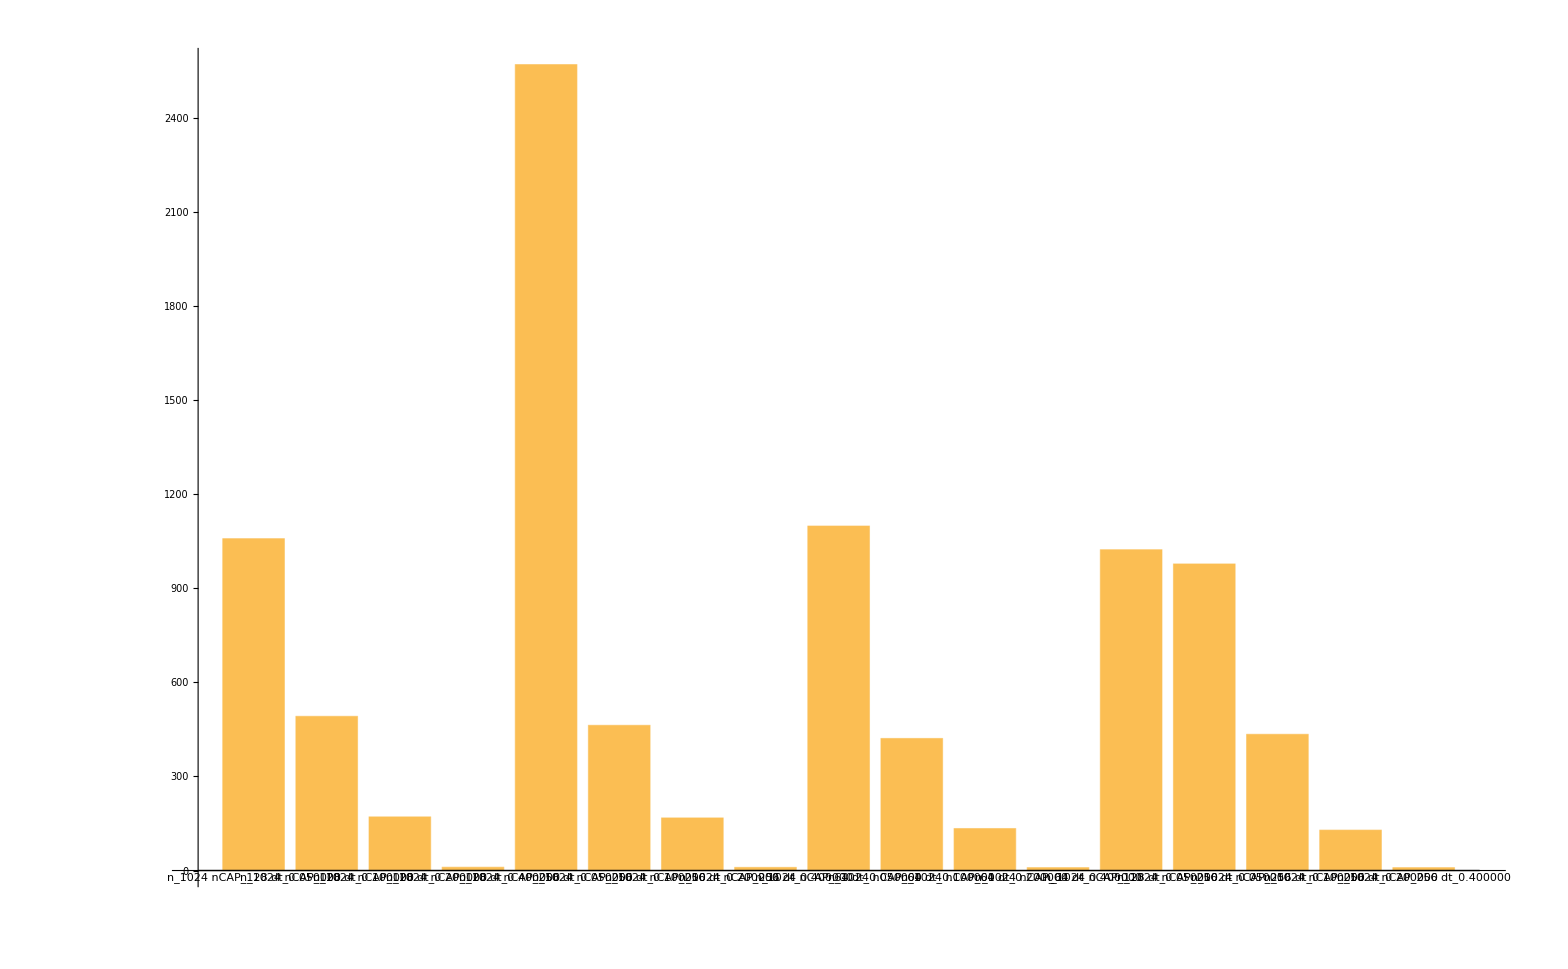

```mathematica
BarChart[ToExpression[StringTrim[Last[StringSplit[#,"|"]]]]&/@Flatten[data[[All,64]]],ChartLabels->(StringRiffle[StringSplit[#,"/"][[{3,4,5(*,6*)}]]]&/@Flatten[data[[All,12]]])]
```

## Older

```mathematica
dir="nitrogen-3e/Results/";
order:=ToExpression@StringExtract[#,"_"->2(*,"i"->1*)]&;
sorted:=SplitBy[SortBy[FileNames[dir<>#],order],order]&;
```

```mathematica
FileNames[dir<>"*final_ionized_joined_P_*.psi*"]
```

{}

```mathematica
ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,Axes->True]&/@FileNames[dir<>"*final_ionized_joined_P_*.psi*"]
```

{-Graphics-}

```mathematica
Print[Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,Axes->True,MaxPlotPoints->48,PlotLabel->FileNameTake[#]]&/@#,4]]&/@sorted@"*during*.psi*";
```

dt=0.1

dt=0.2